Are these the same?

```mathematica
vNeg1[phiBar_Real,kappa_Real]:=BetaRegularized[phiBar/(kappa-3/2),3/2,kappa-1/2]
```

```mathematica
v0[phiBar_Real,kappa_Real]:=Gamma[kappa+1]/(Gamma[kappa-1/2]Gamma[3/2])NIntegrate[t^(1/2)(1-t)^(kappa-3/2),{t,0,phiBar/(kappa-3/2)}]
```

```mathematica
v1[phiBar_Real,kappa_Real]:=Gamma[kappa+1]/((kappa-3/2)^(3/2)Gamma[kappa-1/2]Gamma[3/2])NIntegrate[u^(1/2)(1-u/(kappa-3/2))^(kappa-3/2),{u,0,phiBar}]
```

```mathematica
v2[phiBar_Real,kappa_Real]:=(2 Gamma[kappa+1])/((kappa-3/2)^(3/2)Gamma[kappa-1/2]Gamma[3/2])NIntegrate[v^2(1-v^2/(kappa-3/2))^(kappa-3/2),{v,0,√phiBar}]
```

```mathematica
spaceFac=0.02;
```

```mathematica
kappaVal=100;
```

```mathematica
plotFuncs={vNeg1[phiBar,#]-spaceFac,v0[phiBar,#],v1[phiBar,#]+spaceFac,v2[phiBar,#]+spaceFac*2}&[kappaVal]
```

{-0.02+vNeg1[phiBar,100],v0[phiBar,100],0.02+v1[phiBar,100],0.04+v2[phiBar,100]}

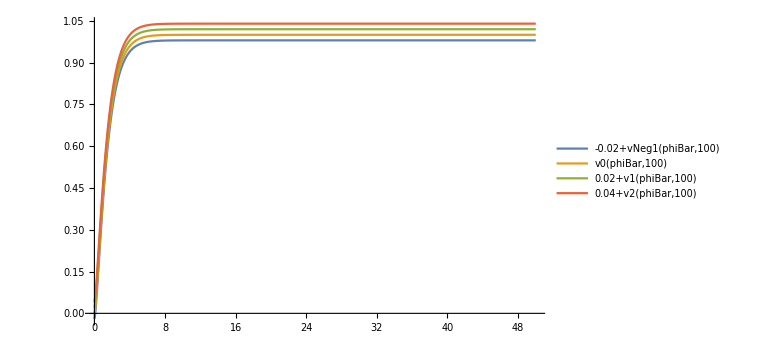

```mathematica
Plot[Evaluate@plotFuncs,{phiBar,0,50},ImageSize->Large,PlotLegends->"Expressions",PlotRange->Full]
```

Play more

```mathematica
func[phiBar_?NumberQ,kappa_?NumberQ]:=(1-phiBar/(kappa-3/2))^(1/2-kappa)
```

```mathematica
func[10,2.4]
```

0.0117243+0.00380947 ⅈ

Compare the Liemohn-and-Khazanov expression obtained formally with the one I got from doing the mu integral first

### Mu integral expression (see journal__20180206__do_n_integral__4__combine_energy_integrals.nb)

```mathematica
densFacKOrig[phiBar_?NumericQ,κ_?NumericQ,RB_?NumericQ]:=1/(16 (-3+2 κ)^(3/2))(-1/(phiBar^2 (-1+RB) Gamma[5/2+κ])√(2/π) Gamma[1+κ] ((-1+RB) (-3+2 κ) (-(-1+RB)^2 (3-2 κ)^2-2 phiBar (-1+RB) (-3+2 κ) (5+2 κ)+4 phiBar^2 (-1+6 κ+4 κ^2))+(2 phiBar+(-1+RB) (-3+2 κ))^3 Hypergeometric2F1[1,1+κ,-1/2,(2 phiBar)/((-1+RB) (3-2 κ))])+8 Csc[π κ] ((3+2 phiBar-2 κ)^-κ √((3+2 phiBar-2 κ)/phiBar) (-3+2 κ)^(1+κ)+(4 √(2 π) Hypergeometric2F1Regularized[-1/2,1,1-κ,(-3+2 κ)/(2 phiBar)])/Gamma[-3/2+κ]));
```

```mathematica
densFacKMod4[phiBar_?NumericQ,κ_?NumericQ,RB_?NumericQ]:=1/(16 (2 κ-3)^(3/2))(-1/(phiBar^2 Gamma[5/2+κ])√(2/π) Gamma[κ+1] (-2 phiBar (RB-1) (2 κ-3)^2 (2 κ+5)+4 phiBar^2(2 κ-3) (4 κ^2+6 κ-1)+(RB-1)^2(2κ-3)^3((phiBar/((RB-1)(κ-3/2))+1)^3 Hypergeometric2F1[1,κ+1,-1/2,-(2 phiBar)/((RB-1) (2 κ-3))]-1))+8 Csc[κ π] ((2κ-3)^(3/2)/phiBar^(1/2)(phiBar/(κ-3/2)-1)^(-κ+1/2)+(4 √(2 π) Hypergeometric2F1Regularized[-1/2,1,-κ+1,(2 κ-3)/(2 phiBar)])/Gamma[κ-3/2]))
```

```mathematica
densFacK[phiBarK_?NumericQ,RB_?NumericQ,κ_?NumericQ]:=1/4( 2 (phiBarK-κ)^(1/2-κ) κ^(-1/2+κ) Csc[π κ]+1/(phiBarK^(3/2) √π √κ)(Gamma[κ]/((-1+RB) Gamma[5/2+κ]) ((-1+RB) κ ((-1+RB)^2 κ^2+phiBarK (-1+RB) κ (5+2 κ)+phiBarK^2 (1-2 κ (3+2 κ)))-(phiBarK+(-1+RB) κ)^3 Hypergeometric2F1[1,1+κ,-1/2,phiBarK/(κ-RB κ)])+(4 phiBarK^2 π Csc[π κ] Hypergeometric2F1Regularized[-1/2,1,1-κ,κ/phiBarK])/Gamma[-1/2+κ]));
```

### Liemohn and Khazanov expression (named LKKappaDensFac[phiBar_,RB_,κ_])

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

### Kappa={2,3,4} expression (journal__20180208__energy_integrals_and_analytic_expression_for....nb)

```mathematica
Keq2[phiBar_,RB_]:=((4 phiBar^2 RB)/((-1+2 phiBar) (-1+2 phiBar+RB))+(√2 √phiBar ArcCos[√2 √phiBar])/(1-2 phiBar)^(3/2)+(√2 √phiBar √(1+(2 phiBar)/(-1+RB)) (-1+RB)^(5/2) ArcSinh[(√2 √phiBar)/(√(-1+RB))])/(-1+2 phiBar+RB)^2)/(√2 √phiBar π)
```

```mathematica
Keq2p5[phiBar_?NumericQ,RB_?NumericQ]:=1/4 phiBar^(3/2) ((-5+2/phiBar^(3/2)+3 phiBar)/(-1+phiBar)^2+(5-3 phiBar-5 RB)/(-1+phiBar+RB)^2)
```

```mathematica
Keq3[phiBar_,RB_]:=((4 √2 phiBar^(3/2) (4 phiBar^2+15 phiBar (-2+RB)-36 (-1+RB)) RB)/((3-2 phiBar)^2 (-3+2 phiBar+3 RB)^2)+(27 ArcCos[√(2/3) √phiBar])/(3-2 phiBar)^(5/2)+(27 √(-1+RB) ArcSinh[(√(2/3) √phiBar)/(√(-1+RB))])/(3+(2 phiBar)/(-1+RB))^(5/2))/(√3 π)
```

```mathematica
Keq4[phiBar_,RB_]:=1/(30 √10 π)(8 phiBar^(3/2) ((1825+2 phiBar (-455+66 phiBar))/(-5+2 phiBar)^3-(60 phiBar^2)/(-5+2 phiBar+5 RB)^3+(110 phiBar)/(-5+2 phiBar+5 RB)^2-73/(-5+2 phiBar+5 RB))+(18750 √2 ArcCos[√(2/5) √phiBar])/(5-2 phiBar)^(7/2)+(18750 √(10+(4 phiBar)/(-1+RB)) (-1+RB)^(9/2) ArcSinh[(√(2/5) √phiBar)/(√(-1+RB))])/(-5+2 phiBar+5 RB)^4)
```

```mathematica
kappa=5;
RB=100.;
```

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

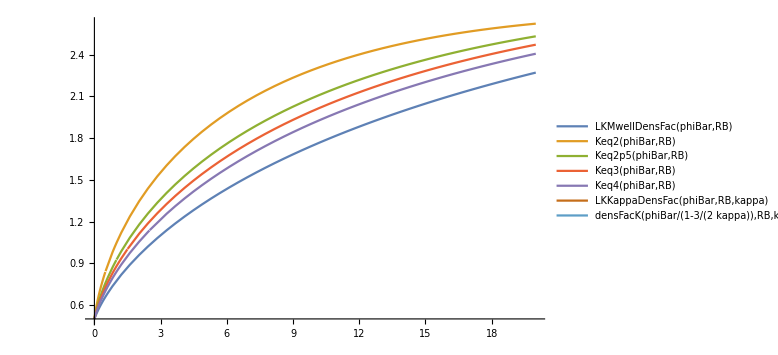

```mathematica
Plot[{LKMwellDensFac[phiBar,RB], Keq2[phiBar,RB],Keq2p5[phiBar,RB],Keq3[phiBar,RB],Keq4[phiBar,RB],LKKappaDensFac[phiBar,RB,kappa],densFacK[phiBar/(1-3/(2 kappa)),RB,kappa]},{phiBar,0,20},PlotLegends->"Expressions",ImageSize->Large]
```

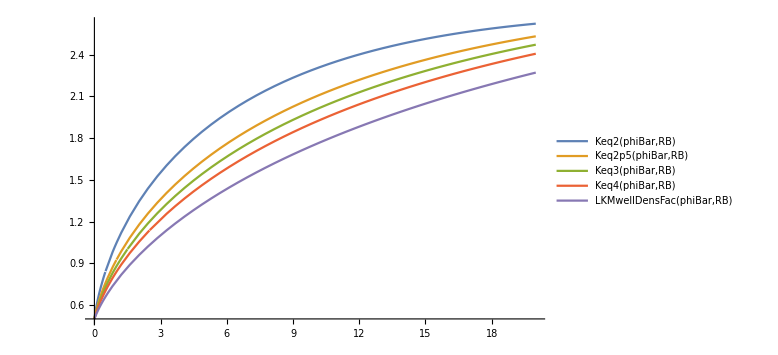

```mathematica
Plot[{ Keq2[phiBar,RB],Keq2p5[phiBar,RB],Keq3[phiBar,RB],Keq4[phiBar,RB],LKMwellDensFac[phiBar,RB]},{phiBar,0,20},PlotLegends->"Expressions",ImageSize->Large]
```